## Section | Beam Splitters and Interferometry

This chapter develops the quantum-optical description of beam splitters and interferometers: it starts by writing the device as a lossless two-port unitary that transforms input mode operators into output modes while preserving bosonic commutators. The formalism reveals hallmark interference phenomena such as the Hong–Ou–Mandel effect, where indistinguishable photon pairs bunch into the same output port, and extends naturally to multi-element arrangements like the Mach–Zehnder interferometer, whose relative-phase control converts path-length differences into measurable intensity fringes or probabilities. An important observation is to notice quantum states have uncertainties even if we use the “most classical” states of light. A brief discussion of polarization is also included.

### Key concepts

Quantum description of beam-splitters

Mode transformation (Heisenberg evolution) and unitary evolution

Mach Zehnder Interferometer (MZI)

Wave- particle duality using single photons

Standard quantum limit

### Quantum Mechanical Description of Beam Splitters

Classically, a lossless beam splitter (BS) can be described as a device with one input mode and two output modes, related to transmitted and reflected amplitudes. However, this description is not adequate in a fully quantum approach because the commutation relations do not hold:

.

A quantum description uses an extra mode that is unused in the classical setup, but in the quantum approach it can have a quantized field in the vacuum state that has relevant physical effects. Using this description, the commutation relations hold, and we can analyze behaviors that cannot be explained classically.

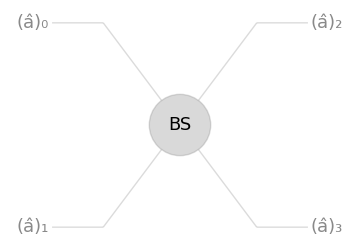
```mathematica
-Graphics--Graphics-
```

The beam splitter can be described as a device with two input modes and two output modes. The field creation operators can be related between input and output modes using the complex reflectance and transmittance coefficients

## Types of Beam Splitters

A general expression for a beam-splitter matrix (that relates input and output modes) can be expressed in terms of reflection, transmission and global phases(ϕ_r, ϕ_t) and the reflectivity (θ) :

Define a general beam-splitter:

```mathematica
GeneralBS = QuantumOperator[ⅇ^(ⅈ ϕg)({{Sin[θ] ⅇ^(ⅈ ϕr), Cos[θ] ⅇ^(-ⅈ ϕt)}, {Cos[θ] ⅇ^(ⅈ ϕt), -Sin[θ] ⅇ^(-ⅈ ϕr)}}),"Parameters"->{θ,ϕg,ϕr,ϕt}];
```

But in practice, two kinds of beam-splitter are used more frequently: dielectric and symmetric beam-splitters. To get 50:50 balanced beam-splitter θ = π/4, and the other phases are set to particular values

Dielectric BS in the 50:50 case we get:

```mathematica
GeneralBS[π/4,0,0,0]
```

1/(√2)00+1/(√2)01+1/(√2)10-1/(√2)11

Symmetric BS ; in the 50:50 case we get:

```mathematica
GeneralBS[π/4,π/2,-π/2,0]
```

1/(√2)00+ⅈ/(√2)01+ⅈ/(√2)10+1/(√2)11

In general in terms of the reflectivity r :

```mathematica
bs1 = GeneralBS[ArcSin[r],0,0,0];
```

Associated matrix t =√(1-r^2):

```mathematica
Normal[(bs1["Matrix"])]/. √(1-r^2)->t//MatrixForm
```

(r | t
t | -r)

The evolution matrix of the beam splitter is unitary:

```mathematica
FullSimplify[SuperDagger[bs1]@bs1,0<r<1]==QuantumOperator["I"]
```

True

### Digression: Polarization of a Photon

The polarization degrees of freedom of a photon can be described in a quantum two-level system, which follows the same mathematical structure as the classical description with Jones vectors.

Define a basis:

```mathematica
polBasis = QuantumBasis[{"H","V"}];
```

An alternative basis is working in the diagonal and antidiagonal basis:

```mathematica
diagPolBasis =QuantumBasis@AssociationThread[{"D","A"}->QuantumBasis["X"]["Elements"]];
```

Change of basis in the Wolfram Quantum Framework:

```mathematica
QuantumState["+",polBasis]
QuantumState[%,diagPolBasis]
```

1/(√2)H+1/(√2)V

D

Example Section.1: Polarization Projection

Project the first photon of the |ψ^-⟩ state in diagonal polarization and plot the amplitudes in a two-photon diagonal-antidiagonal basis

Create state:

```mathematica
psiminus = QuantumState["PsiMinus",polBasis]
```

1/(√2)HV-1/(√2)VH

Project the first photon (this means using a polarizer or projector |D⟩ ⟨ D |):

```mathematica
projectionD =QuantumState["0",diagPolBasis]["Projector"]@QuantumState["PsiMinus",polBasis]
```

-1/2DH+1/2 DV

Use "AmplitudesPlot", only |DA⟩ nonzero amplitude:

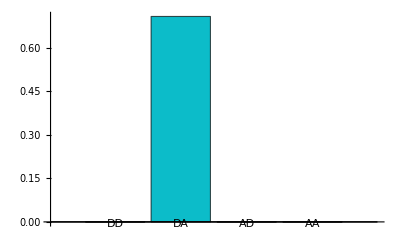

```mathematica
QuantumState[projectionD,QuantumBasis[{diagPolBasis,diagPolBasis}]]["AmplitudesPlot",ChartLegends->Automatic]
```

#### Wave plates

To change the polarization, we can use wave plates made of birefringent materials.

Half- and quarter-wave plate (HWP and QWP) definitions in the H and V polarization basis

Half-wave plate at angle θ:

```mathematica
TraditionalForm[mat1=RotationMatrix[θ].{{1,0},{0,ⅇ^(ⅈ π)}}.RotationMatrix[-θ]//Simplify]
```

(cos(2 θ) | sin(2 θ)
sin(2 θ) | -cos(2 θ))

Quarter-wave plate at angle θ:

```mathematica
TraditionalForm[mat2 =RotationMatrix[θ].{{1,0},{0,ⅇ^(ⅈ π/2)}}.RotationMatrix[-θ]//Simplify]
```

(cos^2(θ)+ⅈ sin^2(θ) | (1-ⅈ) sin(θ) cos(θ)
(1-ⅈ) sin(θ) cos(θ) | sin^2(θ)+ⅈ cos^2(θ))

Wrapping matrices in QuantumOperators:

```mathematica
HWP = QuantumOperator[mat1,polBasis,"Parameters"->θ];
QWP = QuantumOperator[mat2,polBasis,"Parameters"->θ];
```

Common single-qubit gates can be implemented by particular angles:

```mathematica
HWP[π/4]==QuantumOperator["X"]
```

True

```mathematica
HWP[π/8]==QuantumOperator["H"]
```

True

Transforming |H⟩ polarization to |V⟩:

```mathematica
HWP[π/4][]
```

V

In general, any operator that belongs to SU(2) in polarization space can be realized with a sequence of QWP-HWP-QWP operations(Reference “Minimal three-component SU(2) gadget for polarization optics”).

### Evolution of Quantum States in Beam Splitters

Define the output modes:

```mathematica
{a2,a3} = Table[AnnihilationOperator[{i}],{i,2}];
```

We use a symmetric 50:50 beam splitter:

```mathematica
balancedBS =GeneralBS[π/4,π/2,-π/2,0];
```

We calculate the inverse because in this case, we find input modes in terms of output modes (Heisenberg-like evolution):

```mathematica
{a0,a1} = Inverse@balancedBS["Matrix"].{a2,a3};
```

Evolution of a one-photon state :

```mathematica
onePhotonEvolve = SuperDagger[a1][]
```

1/(√2)01+ⅈ/(√2)10

The output state results in a entangled state see QuantumEntanglementMonotone (default metric is “Concurrence”):

```mathematica
QuantumEntanglementMonotone[onePhotonEvolve,{1,2}]
```

1

If we put one photon in each of the input ports, the two photons emerge together. That is explained by interference when the photons are indistinguishable (Hong–Ou–Mandel effect)

State will evolve as :

```mathematica
twoPhotonEvolve = SuperDagger[a0]@SuperDagger[a1][]
```

ⅈ/(√2)02+ⅈ/(√2)20

There is also possible to adopt a Schrodinger picture approach and for the 50:50 symmetric beam splitter we have the unitary

Define the modes:

```mathematica
{a0,a1} = Table[AnnihilationOperator[{i}],{i,2}];
```

Calculate the unitary operator representing the beam-splitter:

```mathematica
U = QuantumOperator[MatrixExp[ⅈ π/4.(SuperDagger[a0]@a1+a0@SuperDagger[a1])],"Label"->"BS"];
```

Representing the evolution as a circuit:

```mathematica
photonEvolve = QuantumCircuitOperator[{FockState[{1,1}],U}];
```

See the diagram:

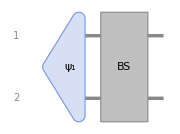

```mathematica
photonEvolve["Diagram",ImageSize->Small]
```

Schrodinger picture evolution:

```mathematica
Chop[photonEvolve[]]
```

(0.+0.707107 ⅈ)02+(0.+0.707107 ⅈ)20

In the QuantumFramework we have  BeamSplitterOperator for doing Schrodinger picture evolution (recurrence method is preferred for symbolic numbers)

```mathematica
balancedsymmetric = BeamSplitterOperator[{π/4,π/2},Method->"Recurrence"];
```

We get the same result:

```mathematica
balancedsymmetric@FockState[{1,1}]
```

ⅈ/(√2)02+ⅈ/(√2)20

Now let’s try using a coherent state in the input port one  using

Numerical amplitude:

```mathematica
αcoh = RandomReal[{1,1.5}]Exp[ⅈ RandomReal[{0,2π}]];
```

Evolve the operators:

```mathematica
{a0,a1} = Inverse@balancedBS["Matrix"].{a2,a3};
```

Output state:

```mathematica
cohBS = MatrixExp[(αcoh a1["Dagger"]-αcoh* a1)][]//Chop;
```

The entanglement monotone is really close to zero, so it is a product state (not entangled):

```mathematica
QuantumEntanglementMonotone[cohBS,{{1},{2}}]
```

0.

The theoretical result represents that a coherent state resembles a classical field that divides evenly in a 50:50 BS (average photon number |α|^2/2 in each output mode and phase shift π/2 for the reflected wave)

Product state:

```mathematica
productState = coherent[ⅈ αcoh/√2] //coherent[αcoh/√2];
```

Evaluate how similar the states are, should be really close to 1:

```mathematica
QuantumSimilarity[cohBS,productState,"Fidelity"]
```

1.

Individual amplitudes have numerical error though, the ones that have bigger numerical error are mostly related to the edge effects of truncation:

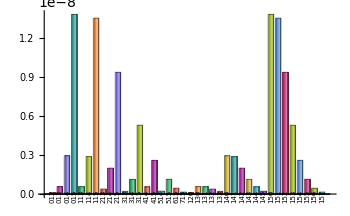

```mathematica
(productState-cohBS)["AmplitudePlot",]
```

Also, the beam splitter causes the transformation that N photons are binomially distributed over the two modes

Let’s verify that for a particular N:

```mathematica
Np = 8;
```

Output state:

```mathematica
outstate = balancedsymmetric[FockState[{0,Np}]]
```

1/16 08+ⅈ/(4 √2)17-(√7)/826-1/4 ⅈ √(7/2)35+(√(35/2))/8 44+1/4 ⅈ √(7/2)53-(√7)/862-ⅈ/(4 √2)71+1/16 80

Probability plot of the output state:

```mathematica
p1 =outstate["ProbabilityPlot",AxesLabel->{"States","Probability"}];
```

Binomial distribution with parameters N_p and p = 0.5:

```mathematica
p2=DiscretePlot[PDF[BinomialDistribution[Np,0.5],k-1],{k,1,Np+1},PlotStyle->{Black,PointSize[0.015]}];
```

Show the result:

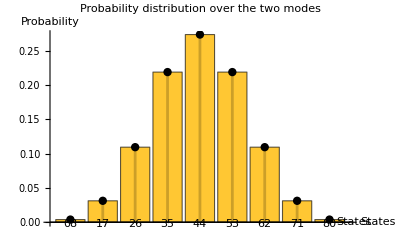

```mathematica
Show[p1,p2,PlotLabel->"Probability distribution over the two modes",ImageSize->400,LabelStyle->12]
```

### Single-Photon Mach–Zehnder Interferometer

Let’s consider the widely used Mach-Zehnder interferometer for the single photon case. The interferometer consists of  two beam-splitters and a phase shift in one of the arms. We can observe that in the following diagram

Set up a small truncation size:

```mathematica
SetFockSpaceSize[3];
```

Now we use a dielectric beam-splitter:

```mathematica
dielectricBS = QuantumOperator[BeamSplitterOperator[{π/4,0}],"Label"->"BS"];
```

Phase shift operator:

```mathematica
phase = QuantumOperator[PhaseShiftOperator[ϕ],"Label"->"ϕ"];
```

Circuit representation of the Mach-Zehnder interferometer arrangement:

```mathematica
MZI =QuantumCircuitOperator[{dielectricBS,phase,dielectricBS}];
```

See the diagram:

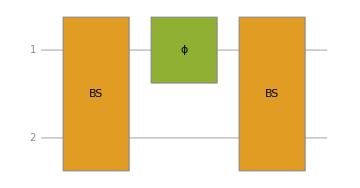

```mathematica
MZI["Diagram","GateBackgroundStyle"->]
```

Calculate the output probabilities:

```mathematica
probs =List@@MZI[FockState[{0,1}]]["Probability"]
```

{(Abs[1/2-ⅇ^(ⅈ ϕ)/2]^2)/(Abs[1/2-ⅇ^(ⅈ ϕ)/2]^2+Abs[-1/2-ⅇ^(ⅈ ϕ)/2]^2),(Abs[-1/2-ⅇ^(ⅈ ϕ)/2]^2)/(Abs[1/2-ⅇ^(ⅈ ϕ)/2]^2+Abs[-1/2-ⅇ^(ⅈ ϕ)/2]^2)}

Simplified probabilities:

```mathematica
simplifiedProbs =Simplify[ComplexExpand[probs//Values],ϕ∈Reals]//TrigReduce
```

{1/2 (1-cos(ϕ)),1/2 (cos(ϕ)+1)}

Plotting probabilities at the detectors:

```mathematica
Plot[Evaluate@MapThread[Callout[#1,#2,Right]&,{simplifiedProbs,{"D1","D2"}}],{ϕ,0,6Pi},
]
```

-Graphics-

Experimentally, this clearly demonstrates wave–particle duality: wave-like behavior is seen because an interference pattern emerges, and particle-like behavior is evident from the discrete detection events. The pattern builds up progressively as many individual photons pass through the interferometer.

### Interference of coherent states

Let’s analyze the interferometry of coherent states in a Mach–Zehnder interferometer. We should expect similar results as using classical light, we will follow a Schrodinger picture evolution approach

Set up parameters:

```mathematica
SetFockSpaceSize[30];
αcoh = 1.8Exp[I RandomReal[{0,2Pi}]];
```

Balanced symmetric BS:

```mathematica
balancedsymmetric = BeamSplitterOperator[{π/4.,π/2.},Method->"Recurrence"];
```

MZI interferometer operator (phase shift θ in second arm):

```mathematica
MZI =balancedsymmetric@PhaseShiftOperator[θ,{2}]@balancedsymmetric;
```

Initial state:

```mathematica
init = FockState[0]//coherent[αcoh];
```

Output state:

```mathematica
out = QuantumState[MZI[init],"Parameters"->θ];
```

Evidently the resulting state is a product state, zero entanglement monotone:

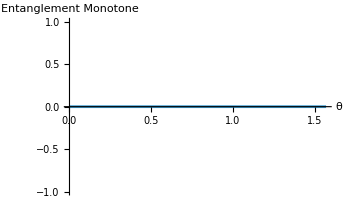

```mathematica
Plot[QuantumEntanglementMonotone[out[θ],{{1},{2}},"Concurrence"],{θ,0,π/2},AxesLabel->{"θ","Entanglement Monotone"}]
```

It can be shown that the analytical expression for the evolution is

.

Product state analytical:

```mathematica
product = QuantumState[(coherent[(ⅈ(1+ⅇ^(ⅈ θ))αcoh)/2]//coherent[(( ⅇ^(ⅈ θ)-1)αcoh)/2]),"Parameters"->θ];
```

Sample phases:

```mathematica
phases = N@Subdivide[0,π/2,25];
```

Compare results, empty “AmplitudeList” represent states are numerically the same up the chosen precision:

```mathematica
Chop[(out[#]-product[#]),10^-9]["AmplitudeList"]&/@phases
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

Phase shift θ can be measured by subtracting the intensities from two detectors, D_1 and D_2. That can be represented by ⟨Ô ⟩ with Ô=c^†c-d^†d  the number difference operator(c and d output modes). This is simple to calculate, because the mean of the number operator on a coherent state is just the magnitude of the complex squared:

Output modes:

```mathematica
{c,d}= Array[AnnihilationOperator[{#}]&,2];
```

Current operator:

```mathematica
Ocurrent = SuperDagger[c]@c -SuperDagger[d]@d;
```

The mean of the Ô operator can be calculated symbolically for each coherent state:

```mathematica
OmeanSymbolic = FullSimplify[Abs[(ⅈ (ⅇ^(ⅈ θ)+1)α)/2]^2-Abs[((ⅇ^(ⅈ θ)-1)α)/2]^2,Element[θ,Reals]]
```

α Conjugate[α] Cos[θ]

Current expectations for varying phases θ:

```mathematica
currentMean =Simplify[Chop[(SuperDagger[out[θ]]@Ocurrent@out[θ])["Scalar"]],θ∈Reals];
```

We can recover θ based on the symbolic expression, of course this is just showing the equivalence in a computational manner, but real measurements will not be perfect:

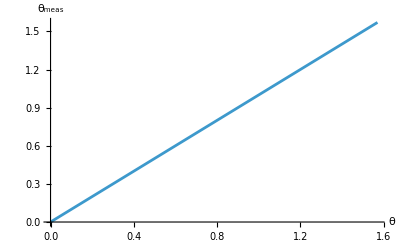

```mathematica
Plot[ArcCos[{Re@currentMean}/Abs[αcoh]^2],{θ,0,π/2},AxesLabel->{"θ"," θ_meas"}]
```

We observe the result analogous to classical coherent light, but coherent states are still quantum states that possess quantum mechanical fluctuations. Using error propagation, the uncertainty of phase measurement is

,

which is optimal or minimum for odd multiples of π/2. That is the best result with classical-like states determining a standard quantum limit. It is possible to beat that limit using non-classical light; for example, that is discussed in large-scale interferometers to detect gravitational waves (LIGO).

#### Initialization

Load quantum framework functions:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load quantum framework functions for the second quantization:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Useful definitions:

```mathematica
a := AnnihilationOperator[]
coherent := CoherentState[]["Normalize"]
```

Vocabulary

BeamSplitterOperator |   | Operator  that performs evolution of states going
through a beam-splitter in the Schrodinger picture
PhaseShiftOperator |   | Applies a phase factor proportional to the photon number
of the Fock state
QuantumEntanglementMonotone |   | calculates a metric to measure entanglement of a
QuantumState, default metric is “Concurrence”

Exercises

Define the basis of circular right |R⟩, and circular left polarization |L⟩ (use any convention)

QuantumBasis@AssociationThread[{"R","L"}->QuantumBasis["Y"]["Elements"]]

<|"R"→{1/(√2),ⅈ/(√2)},"L"→{1/(√2),-ⅈ/(√2)}|>

QuantumBasis[<|"R"->1/(√2){1, ⅈ},"L"->1/(√2){1,-ⅈ}|>]

<|"R"→{1/(√2),ⅈ/(√2)},"L"→{1/(√2),-ⅈ/(√2)}|>

Check the state |3,1⟩ after a balanced beam-splitter operation has a uniform Fock state distribution

BeamSplitterOperator[{π/4.,π/2.}][FockState[{3,1}]]["ProbabilityPlot"]